```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*WHITE DWARF NUCLEI*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
Nn=4/3*π *R^3*n;
sigmasat=(π*R^2)/Nn;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
teq[mx_,sigma_,sigmadmdm_,T_,anncross_]:=2/((b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5);
```

```mathematica
ldm[mx_,sigma_,sigmadmdm_,T_,anncross_]:=mx*(a[mx,sigma]+b[mx,sigmadmdm]*(b[mx,sigmadmdm]+(b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5)/(2*anncross/vth[mx,T]));
```

```mathematica
myticks={{Automatic,None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

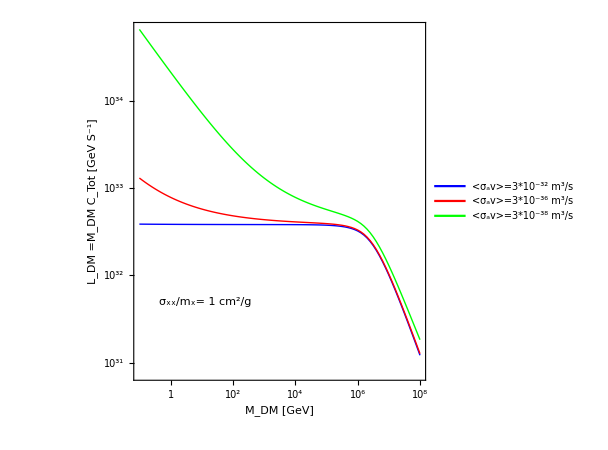

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-32]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-36]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameTicks->myticks,PlotLegends->Placed[{"<σ_av>=3*10^-32 m^3/s","<σ_av>=3*10^-36 m^3/s","<σ_av>=3*10^-38 m^3/s"},{0.8,0.9}],Epilog->Style[Text["σ_xx/m_x= 1 cm^2/g",Log@{3.0,0.5*10^32}],15],FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DM \ C_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]
```

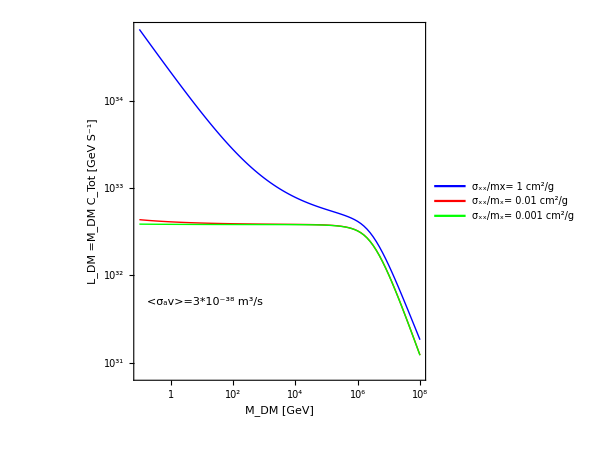

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,(0.01*10^x)/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,(0.001*10^x)/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameTicks->myticks,PlotLegends->Placed[{"σ_xx/mx= 1 cm^2/g","σ_xx/m_x= 0.01 cm^2/g","σ_xx/m_x= 0.001 cm^2/g"},{0.8,0.8}],Epilog->Style[Text["<σ_av>=3*10^-38 m^3/s",Log@{3.0,0.5*10^32}],15],FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DM \ C_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]
```

```mathematica
anncross=3*10^-32;(*in m^3/sec*)
mx=10^-2;
```

```mathematica
mx*a[mx,sigmasat]
```

1.7665×10^32

```mathematica
mx*b[mx,mx/(5.62*10^27)]*(b[mx,mx/(5.62*10^27)]+(b[mx,mx/(5.62*10^27)]^2+4*a[mx,sigmasat]*anncross/vth[mx,10^7])^0.5)/(2*anncross/vth[mx,10^7])
```

6.16305×10^30

```mathematica
anncross=3*10^-41;(*in m^3/sec*)
mx=10^-2;
```

```mathematica
mx*a[mx,sigmasat]
```

1.7665×10^32

```mathematica
mx*b[mx,mx/(5.62*10^27)]*(b[mx,mx/(5.62*10^27)]+(b[mx,mx/(5.62*10^27)]^2+4*a[mx,sigmasat]*anncross/vth[mx,10^7])^0.5)/(2*anncross/vth[mx,10^7])
```

2.07771×10^38

```mathematica
(*when the annihilation cross section is low then the self capture term is dominating but for thermal relic cross section (annihilation cross section is not so low) ordinary capture is dominating*)
```

```mathematica
(*hence the result in first plot is quite same with the ordinary capture graph as expected, but  the second plot looks different for the new terms*)
```

```mathematica
LTData=Import["C:\\Users\\Anupam\\Desktop\\DM SELF\\Book.csv"];
```

```mathematica
σ0=5.67*10^-8;
```

```mathematica
temp=LTData[[All,1]];
Lum=LTData[[All,2]]/10^28;
```

```mathematica
radi=((LTData[[All,2]]*1.602*10^-10)/(4*π*σ0*(LTData[[All,1]]*10^3)^4))^0.5/10^6;
min=Min[temp];
```

```mathematica
max=Max[temp];
```

```mathematica
col=(temp-min)/(max-min);
```

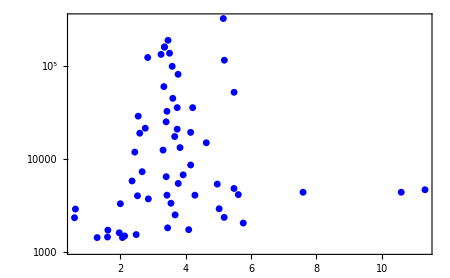

```mathematica
ListLogPlot[Table[{radi[[i]],Lum[[i]]},{i,Length[radi]}],PlotRange->All,Joined->False,PlotStyle->Blue,Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],ImageSize->450]
```

```mathematica
(*WHITE DWARF NUCLEI FOR DIFFERENT RADIUS*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
Nn[R_]:=4/3*π *R^3*n;
sigmasat[R_]:=(π*R^2)/Nn[R];
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
a[mx_,sigma_,R_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat[R]]*Min[1,δp[mx]/pf]*vbar*Nn[R]*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
ldm[mx_,sigma_,sigmadmdm_,T_,anncross_,R_]:=mx*(a[mx,sigma,R]+b[mx,sigmadmdm]*(b[mx,sigmadmdm]+(b[mx,sigmadmdm]^2+4*a[mx,sigma,R]*anncross/vth[mx,T])^0.5)/(2*anncross/vth[mx,T]));
```

```mathematica
rlist=Subdivide[0.1,11.3169,5000];
```

```mathematica
lum={};
lum1={};
lum2={};
Do[
m=rlist[[i]];
AppendTo[lum,ldm[0.4,10^-42,0.4/(5.62*10^27),10^6,10^-38,m*10^6]];
AppendTo[lum1,ldm[0.4,10^-42,(0.1*0.4)/(5.62*10^27),10^6,10^-38,m*10^6]];
AppendTo[lum2,ldm[0.4,10^-42,(10^-4*0.4)/(5.62*10^27),10^6,10^-38,m*10^6]];
,{i,Length[rlist]}]
```

```mathematica
LDMtable=Table[{rlist[[i]],10^-28*lum[[i]]},{i,Length[rlist]}];
LDMtable1=Table[{rlist[[i]],10^-28*lum1[[i]]},{i,Length[rlist]}];
```

```mathematica
LDMtable2=Table[{rlist[[i]],10^-28*lum2[[i]]},{i,Length[rlist]}];
```

```mathematica
(*Export["sigmapsigmasat.csv",LDMtable];*)
```

```mathematica
ra=LDMtable[[All,1]];
```

```mathematica
lumi=LDMtable[[All,2]];
lumi1=LDMtable1[[All,2]];
lumi2=LDMtable2[[All,2]];
```

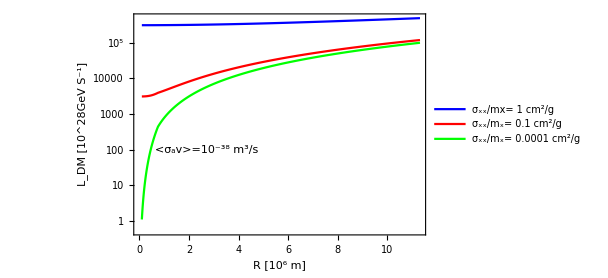

```mathematica
ListLogPlot[{Table[{ra[[i]],lumi[[i]]},{i,Length[rlist]}],Table[{ra[[i]],lumi1[[i]]},{i,Length[rlist]}],Table[{ra[[i]],lumi2[[i]]},{i,Length[rlist]}]},PlotRange->All,Joined->True,PlotStyle->{Blue,Red,Green},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],PlotLegends->Placed[{"σ_xx/mx= 1 cm^2/g","σ_xx/m_x= 0.1 cm^2/g","σ_xx/m_x= 0.0001 cm^2/g"},{0.8,0.25}],Epilog->Style[Text["<σ_av>=10^-38 m^3/s",Log@{15.0,100}],15],FrameLabel->{Style[" R [10^6 m]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM [10^28GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},ImageSize->450]
```

```mathematica
(*WHITE DWARF NUCLEI FOR DIFFERENT RADIUS*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
Nn[R_]:=4/3*π *R^3*n;
sigmasat[R_]:=(π*R^2)/Nn[R];
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
a[mx_,sigma_,R_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat[R]]*Min[1,δp[mx]/pf]*vbar*Nn[R]*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
ldm[mx_,sigma_,sigmadmdm_,T_,anncross_,R_]:=mx*(a[mx,sigma,R]+b[mx,sigmadmdm]*(b[mx,sigmadmdm]+(b[mx,sigmadmdm]^2+4*a[mx,sigma,R]*anncross/vth[mx,T])^0.5)/(2*anncross/vth[mx,T]));
```

```mathematica
rlist=Subdivide[0.1,11.3169,5000];
```

```mathematica
lum={};
lum1={};
lum2={};
Do[
m=rlist[[i]];
AppendTo[lum,ldm[10,sigmasat[m],10/(5.62*10^27),10^6,10^-34,m*10^6]];
AppendTo[lum1,ldm[10,10^-44,10/(5.62*10^27),10^6,10^-34,m*10^6]];
AppendTo[lum2,ldm[10,10^-46,10/(5.62*10^27),10^6,10^-34,m*10^6]];
,{i,Length[rlist]}]
```

```mathematica
LDMtable=Table[{rlist[[i]],10^-28*lum[[i]]},{i,Length[rlist]}];
LDMtable1=Table[{rlist[[i]],10^-28*lum1[[i]]},{i,Length[rlist]}];
```

```mathematica
LDMtable2=Table[{rlist[[i]],10^-28*lum2[[i]]},{i,Length[rlist]}];
```

```mathematica
(*Export["sigmapsigmasat.csv",LDMtable];*)
```

```mathematica
ra=LDMtable[[All,1]];
```

```mathematica
lumi=LDMtable[[All,2]];
lumi1=LDMtable1[[All,2]];
lumi2=LDMtable2[[All,2]];
```

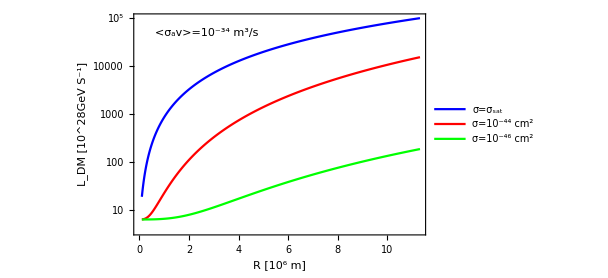

```mathematica
ListLogPlot[{Table[{ra[[i]],lumi[[i]]},{i,Length[rlist]}],Table[{ra[[i]],lumi1[[i]]},{i,Length[rlist]}],Table[{ra[[i]],lumi2[[i]]},{i,Length[rlist]}]},PlotRange->All,Joined->True,PlotStyle->{Blue,Red,Green},Frame->True,FrameStyle->Directive[Black,16,FontFamily->"Times"],PlotLegends->Placed[{"σ=σ_sat","σ=10^-44 cm^2","σ=10^-46 cm^2"},{0.8,0.15}],Epilog->Style[Text["<σ_av>=10^-34 m^3/s",Log@{15.0,0.5*10^5}],15],FrameLabel->{Style[" R [10^6 m]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM [10^28GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},ImageSize->450]
```

```mathematica
(*WHITE DWARF *)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;

b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
```

```mathematica
teq[mx_,sigmadmdm_,T_,anncross_]:=2/b[mx,sigmadmdm];
```

```mathematica
ldm[mx_,sigmadmdm_,T_,anncross_]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
(*ContourPlot[{ldm[10^x,0.0,10^y,10^7,10^-41]==2.05*10^31,10^y/10^x==1/(5.62*10^27)},{x,-3,6},{y,-20,-36},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]*)
```

```mathematica
p=ContourPlot[{ldm[10^x,10^y,10^7,3*10^-38]==2.05*10^31},{x,-3,6},{y,-20,-36},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500];
```

```mathematica
points=Catenate@Cases[Normal@p,Line[pts_]->pts,Infinity];
```

```mathematica
mchi=10^points[[All,1]];
sigmachi=10^points[[All,2]];
```

```mathematica
ratio=10^points[[All,2]]/10^points[[All,1]]*10^28/1.78;
```

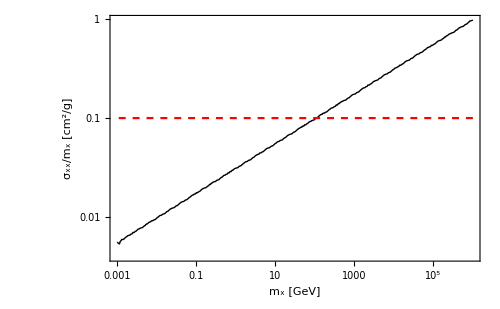

```mathematica
ListLogLogPlot[{Table[{mchi[[i]],ratio[[i]]},{i,Length[mchi]}],Table[{mchi[[i]],0.1},{i,Length[mchi]}]},PlotRange->All,Joined->True,PlotStyle->{{Thick,Black},{Dashed,Red}},Frame->True,AxesOrigin->{0.001,Automatic},FrameStyle->Directive[Black,16,FontFamily->"Times"],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx/m_x [cm^2/g]",FontSize->20,Bold]},ImageSize->500]
```

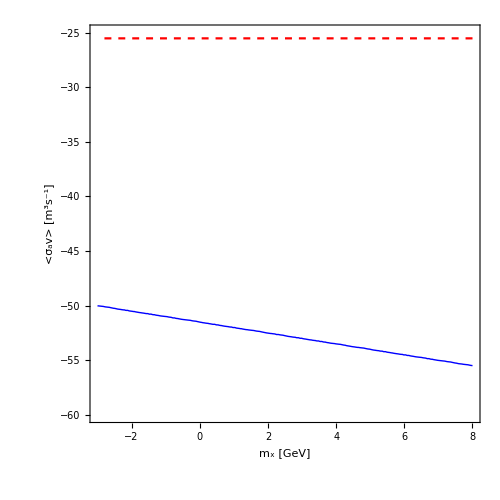

```mathematica
ContourPlot[{ldm[10^x 10^6,10^x/(5.62*10^28),10^7,10^y]==2.05*10^31,y==Log10[3*10^-26]},{x,-3,8},{y,-25,-60},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [m^3s^-1]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
(*ANALYSIS IN THE <Subscript[σ, a] v> - Subscript[m, χ] plane *)
```

```mathematica
(*SUN *)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
vtilde=247*10^3;(*in m/sec*)
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=162.2*10^3;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;

fMBboosted[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ; 
(*b[mx_,sigmadmdm_]:=sigmadmdm*vesc^2*(√(3/2) √(1/vbar^2) ρx Erf[η])/(mx η)-sigmadmdm*(ⅇ^(-η^2) ρx (2 η+ⅇ^(η^2) √π (1+2 η^2) Erf[η]))/(mx √(6 π) √(1/vbar^2) η);*)
b[mx_,sigmadmdm_]:=sigmadmdm*ρx/mx*NIntegrate[fMBboosted[u]/u*(vesc^2-u^2),{u,0,vesc},MaxRecursion->12];

teq[mx_,sigmadmdm_,T_,anncross_]:=2/b[mx,sigmadmdm];
```

```mathematica
ldm[mx_,sigmadmdm_,T_,anncross_]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
myticks={{{{-30,"10^-24"},{-40,"10^-34"},{-50,"10^-44"},{-60,"10^-54"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

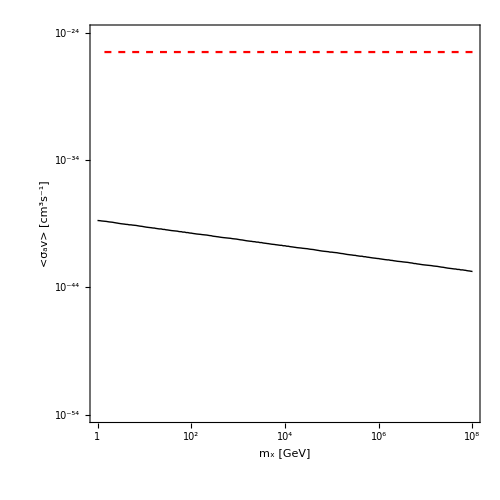

```mathematica
ContourPlot[{ldm[10^x,10^x/(5.62*10^27),10^7,10^y]==2.38*10^36,y==Log10[3*10^-32]},{x,0,8},{y,-30,-60},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Black},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [cm^3s^-1]",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500]
```

```mathematica
(*Below 1 GeV dark matter particle will escape during thermalization for Sun.*)
```

```mathematica
(*SUN WITH GENERALIZED PROBABILITY DISTRIBUTION*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
vtilde=247*10^3;(*in m/sec*)
```

```mathematica
η=((3*vtilde^2)/(2*vbar^2))^0.5;
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=162.2*10^3;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;

mphi=1;
c=3*10^8;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
g1[u_,mx_]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));
```

```mathematica
b[mx_?NumericQ,sigmadmdm_?NumericQ]:=sigmadmdm*NIntegrate[fMBboosted[u,mx]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc},MaxRecursion->12];
```

```mathematica
ldm[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,anncross_?NumericQ]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
teq[mx_,sigmadmdm_,T_,anncross_]:=2/b[mx,sigmadmdm];
```

```mathematica
myticks={{{{-30,"10^-24"},{-40,"10^-34"},{-50,"10^-44"},{-60,"10^-54"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

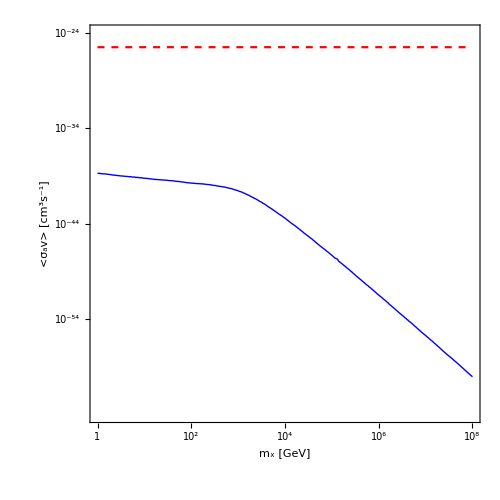

```mathematica
ContourPlot[{ldm[10^x,10^x/(5.62*10^27),10^7,10^y]==2.38*10^36,y==Log10[3*10^-32]},{x,0,8},{y,-30,-70},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [cm^3s^-1]",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

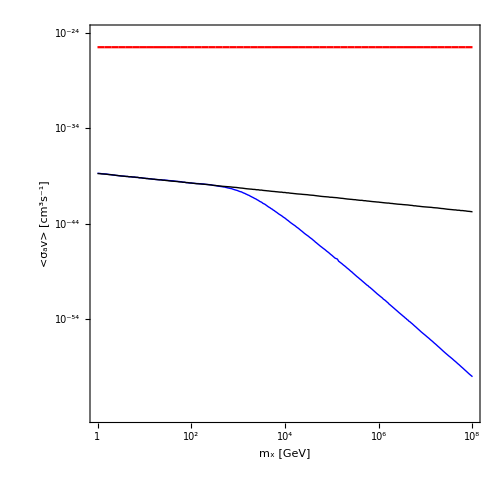

```mathematica
p=Show[-Graphics-,-Graphics-]
```

```mathematica
Export["SUN.pdf",p];
```

```mathematica
(*ANALYSIS IN THE <Subscript[σ, a] v> - Subscript[m, χ] plane *)
```

```mathematica
(*WHITE DWARF *)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
fMBboosted[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ; 

b[mx_,sigmadmdm_]:=sigmadmdm*ρx/mx*NIntegrate[fMBboosted[u]/u*(vesc^2-u^2),{u,0,vesc}];
```

```mathematica
ldm[mx_,sigmadmdm_,T_,anncross_]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
teq[mx_,sigmadmdm_,T_,anncross_]:=2/b[mx,sigmadmdm];
```

```mathematica
myticks={{{{-30,"10^-24"},{-40,"10^-34"},{-50,"10^-44"},{-60,"10^-54"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

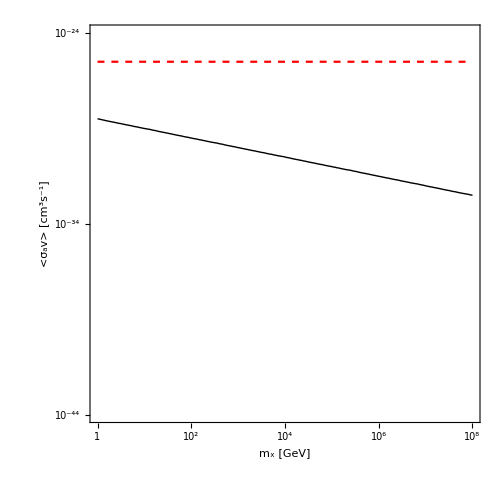

```mathematica
ContourPlot[{ldm[10^x,10^x/(5.62*10^27),10^7,10^y]==2.05*10^31,y==Log10[3*10^-32]},{x,0,8},{y,-30,-50},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,ContourStyle->{{Thick,Black},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [cm^3s^-1]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
(*We have assumed the target particle is at rest. It is true when the velocity of the incoming particle is much higher than the thermal velocity of the target particle. Now the thermal velocity of DM particle with mass 1 GeV is 480 km/sec which is very less with respect to the velocity of the incoming particle. Increasing DM mass will lower the thermal velocity and the calculation will become more reasonable. Though the evaporation mass for WD is ~ 6 MeV*)
```

```mathematica
(*WHITE DWARF WITH GENERALIZED PROBABILITY DISTRIBUTION*)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
c=3*10^8;


mphi=10^-1;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
g1[u_,mx_]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));
```

```mathematica
b[mx_?NumericQ,sigmadmdm_?NumericQ]:=sigmadmdm*NIntegrate[fMBboosted[u,mx]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc},MaxRecursion->12];
```

```mathematica
teq[mx_,sigmadmdm_,T_,anncross_]:=2/b[mx,sigmadmdm];
```

```mathematica
ldm[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,anncross_?NumericQ]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
myticks={{{{-30,"10^-24"},{-40,"10^-34"},{-50,"10^-44"},{-60,"10^-54"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

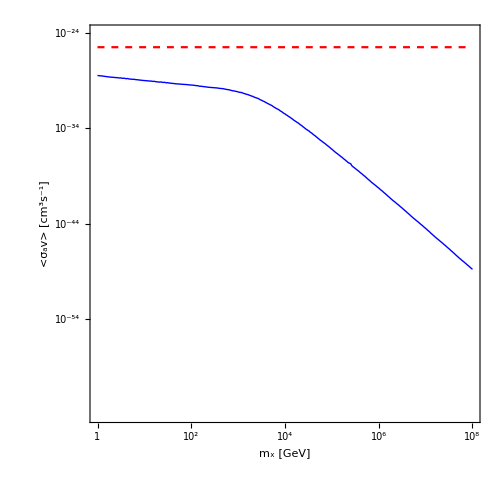

```mathematica
ContourPlot[{ldm[10^x,10^x/(5.62*10^27),10^7,10^y]==2.05*10^31,y==Log10[3*10^-32]},{x,0,8},{y,-30,-70},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [cm^3s^-1]",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,ImageSize->500]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

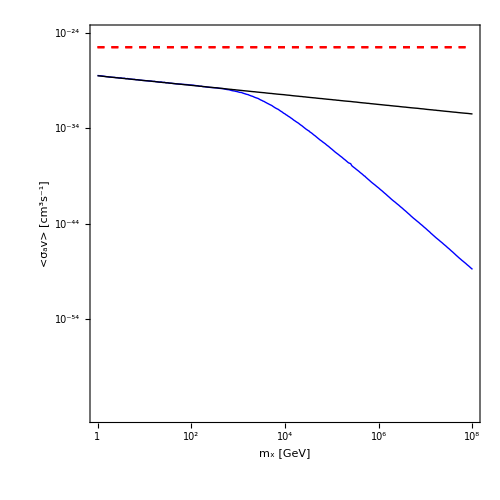

```mathematica
q=Show[-Graphics-,-Graphics-]
```

```mathematica
Export["WD.pdf",q];
```

```mathematica
(*ROUGH*)
g1tilde[u_,mx_]:=(mphi^2*vesc^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(u/c)^2);
e1tilde[u_,mx_]:=(mphi^2*u^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(vesc/c)^2);
Solve[g1tilde[u,mx]-e1tilde[u ,mx]==0,u]

Solve[g1tilde[u,mx]-e1tilde[u ,mx]==1,u]
```

{{u→-vesc},{u→vesc},{u→-(√(-c^2 mphi^2-mx^2 vesc^2))/mx},{u→(√(-c^2 mphi^2-mx^2 vesc^2))/mx}}

{{u→0},{u→0},{u→-(√(-2 c^4 mphi^4-2 c^2 mphi^2 mx^2 vesc^2-mx^4 vesc^4))/(√(2 c^2 mphi^2 mx^2+mx^4 vesc^2))},{u→(√(-2 c^4 mphi^4-2 c^2 mphi^2 mx^2 vesc^2-mx^4 vesc^4))/(√(2 c^2 mphi^2 mx^2+mx^4 vesc^2))}}

```mathematica
fMBboosted[u_,mx_]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2]*Exp[-η^2]*Sinh[2 *(√(3/(2 vbar^2))*u) *η]/(2*(√(3/(2 vbar^2))*u) *η) ;
```

```mathematica
Integrate[fMBboosted[u,mx]*u,{u,0,∞}]//FullSimplify
```

ConditionalExpression[(ⅇ^(-η^2) ρx (2 η+ⅇ^(η^2) √π (1+2 η^2) Erf[η]))/(mx √(6 π) √(1/vbar^2) η),Re[vbar^2]>0]

```mathematica
Integrate[fMBboosted[u,mx]*u^-1,{u,0,∞}]//FullSimplify
```

ConditionalExpression[(√(3/2) √(1/vbar^2) ρx Erf[η])/(mx η),Re[vbar^2]>0]

```mathematica
Integrate[1/((a*z)+b)^2,{z,0,1},Assumptions->a>0&&b>0&&zmin<1]
```

1/(a b+b^2)

```mathematica
Integrate[1/((a*z)+b)^2,{z,zmin,zmax},Assumptions->a>0&&b>0&&zmin<1&&zmax<1]
```

ConditionalExpression[(zmax-zmin)/((b+a zmax) (b+a zmin)),zmax>zmin]

```mathematica
Integrate[1/((a*z)+b)^2,{z,zmin,1},Assumptions->a>0&&b>0&&zmin<1]
```

(1-zmin)/((a+b) (b+a zmin))

```mathematica
Integrate[1/((a*z)+b)^2,{z,0,zmax},Assumptions->a>0&&b>0&&zmax<1&&zmax>0]
```

zmax/(b^2+a b zmax)

```mathematica
g1[u_]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));
```

```mathematica
Solve[g1[u]==0,u]
```

{{u→-vesc},{u→vesc},{u→-(√(-c^2 mphi^2-mx^2 vesc^2))/mx},{u→(√(-c^2 mphi^2-mx^2 vesc^2))/mx}}

```mathematica
Solve[g1[u]==1,u]
```

{{u→0},{u→0},{u→-(√(-2 c^4 mphi^4-2 c^2 mphi^2 mx^2 vesc^2-mx^4 vesc^4))/(√(2 c^2 mphi^2 mx^2+mx^4 vesc^2))},{u→(√(-2 c^4 mphi^4-2 c^2 mphi^2 mx^2 vesc^2-mx^4 vesc^4))/(√(2 c^2 mphi^2 mx^2+mx^4 vesc^2))}}

```mathematica
FullSimplify[(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2))-(mphi^2*vesc^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(u/c)^2)-vesc^2/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/(mphi^2+mx^2*(vesc/c)^2)+1]
```

0

```mathematica
FullSimplify[vesc^2/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/(mphi^2+mx^2*(vesc/c)^2)+(mphi^2*u^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(vesc/c)^2)]
```

1

```mathematica
FullSimplify[vesc^2/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/(mphi^2+mx^2*(vesc/c)^2)-(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2))]
```

(u^2 (c^2 mphi^2+mx^2 (u^2+vesc^2)))/((c^2 mphi^2+mx^2 u^2) (u^2+vesc^2))

```mathematica
FullSimplify[(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2))+(mphi^2*u^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(vesc/c)^2)+u^2/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/(mphi^2+mx^2*(u/c)^2)]
```

1

```mathematica
FullSimplify[(mphi^2*vesc^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(u/c)^2)-(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2))-(mphi^2*u^2)/(vesc^2+u^2)1/(mphi^2+mx^2*(vesc/c)^2)]
```

0

```mathematica
g1[u_]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+4*mr[mx]^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
Solve[g1[u]==0,u]
```

{{u→-(vesc √βplus[mx])/(√(1-βplus[mx]))},{u→(vesc √βplus[mx])/(√(1-βplus[mx]))}}

```mathematica
Solve[g1[u]==1,u]
```

{{u→0},{u→0},{u→-(√(-c^2 mphi^2-4 vesc^2 mr[mx]^2))/(2 mr[mx])},{u→(√(-c^2 mphi^2-4 vesc^2 mr[mx]^2))/(2 mr[mx])}}

```mathematica
(*USEFUL CHECKS*)
```

```mathematica
kb=1.38*10^-23;
T=10^7;
vcarbon=((3*kb*T)/(12*1.78*10^-27))^0.5/1000
```

139.219

```mathematica
vxmax=((3*kb*T)/(10^0*1.78*10^-27))^0.5/1000
```

482.27

```mathematica
vxmin=((3*kb*T)/(10^8*1.78*10^-27))^0.5/1000
```

0.048227

```mathematica
mevapwd=(3*kb*T)/((6*10^6)^2)*5.62*10^26*1000(*in MeV*)
```

6.463

```mathematica
mevapsun=(3*kb*T)/((618*10^3)^2)*5.62*10^26(*in GeV*)
```

0.6092

```mathematica
(*ANALYSIS IN THE Subscript[σ, χχ] - Subscript[m, χ] plane *)
```

```mathematica
(*WHITE DWARF *)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
fMBboosted[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ; 

b[mx_,sigmadmdm_]:=sigmadmdm*ρx/mx*NIntegrate[fMBboosted[u]/u*(vesc^2-u^2),{u,0,vesc}];
```

```mathematica
ldm[mx_,sigmadmdm_,T_,anncross_]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
p=ContourPlot[{ldm[10^x,10^y,10^7,3*10^-32]==2.05*10^31},{x,-2,5},{y,-20,-36},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20];
```

```mathematica
points=Catenate@Cases[Normal@p,Line[pts_]->pts,Infinity];
```

```mathematica
mchi=10^points[[All,1]];
sigmachi=10^points[[All,2]];
```

```mathematica
ratio=10^points[[All,2]]/10^points[[All,1]]*10^28/1.78;
```

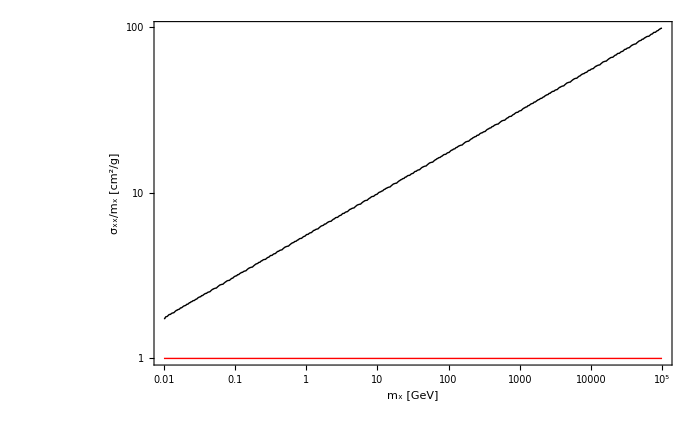

```mathematica
ListLogLogPlot[{Table[{mchi[[i]],ratio[[i]]},{i,Length[mchi]}],Table[{mchi[[i]],1},{i,Length[mchi]}]},PlotRange->All,Joined->True,PlotStyle->{{Thick,Black},{Thick,Red}},PlotRangePadding->None,Frame->True,AxesOrigin->{0.01,Automatic},FrameStyle->Directive[Black,16,FontFamily->"Times"],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx/m_x [cm^2/g]",FontSize->20,Bold]},ImageSize->700]
```

```mathematica
(*We have assumed the target particle is at rest. It is true when the velocity of the incoming particle is much higher than the thermal velocity of the target particle. Now the thermal velocity of DM particle with mass 1 GeV is 480 km/sec which is very less with respect to the velocity of the incoming particle. Increasing DM mass will lower the thermal velocity and the calculation will become more reasonable. Though the evaporation mass for WD is ~ 6 MeV*)
```

```mathematica
(*WHITE DWARF WITH GENERALIZED PROBABILITY DISTRIBUTION*)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
c=3*10^8;


mphi=10^-1;
```

```mathematica
fMBboosted[u_?NumericQ,mx_?NumericQ]:=ρx/mx*(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
g1[u_,mx_]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));
```

```mathematica
b[mx_?NumericQ,sigmadmdm_?NumericQ]:=sigmadmdm*NIntegrate[fMBboosted[u,mx]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc},MaxRecursion->12];
```

```mathematica
teq[mx_,sigmadmdm_]:=2/b[mx,sigmadmdm];
```

```mathematica
ldm[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,anncross_?NumericQ]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
p=ContourPlot[{ldm[10^x,10^y,10^7,3*10^-32]==2.05*10^31},{x,-2,6},{y,-20,-36},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->20];
```

```mathematica
points=Catenate@Cases[Normal@p,Line[pts_]->pts,Infinity];
```

```mathematica
mchi=10^points[[All,1]];
sigmachi=10^points[[All,2]];
```

```mathematica
ratio=10^points[[All,2]]/10^points[[All,1]]*10^28/1.78;
```

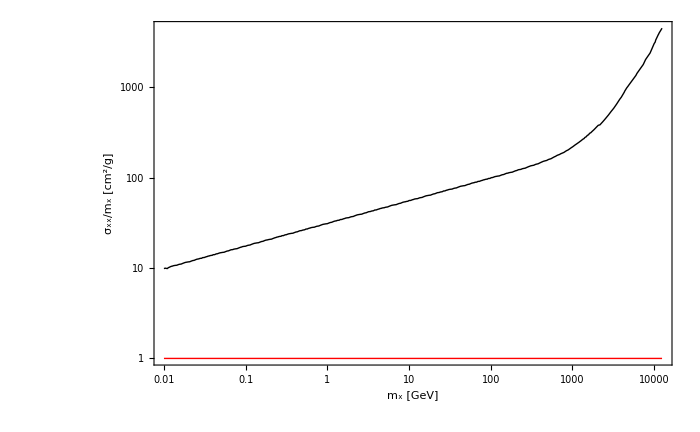

```mathematica
ListLogLogPlot[{Table[{mchi[[i]],ratio[[i]]},{i,Length[mchi]}],Table[{mchi[[i]],1},{i,Length[mchi]}]},PlotRange->All,Joined->True,PlotStyle->{{Thick,Black},{Thick,Red}},PlotRangePadding->None,Frame->True,AxesOrigin->{0.01,Automatic},FrameStyle->Directive[Black,16,FontFamily->"Times"],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx/m_x [cm^2/g]",FontSize->20,Bold]},ImageSize->700]
```

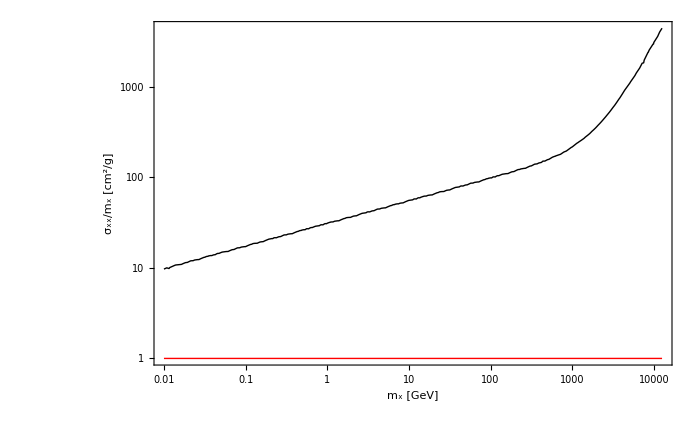
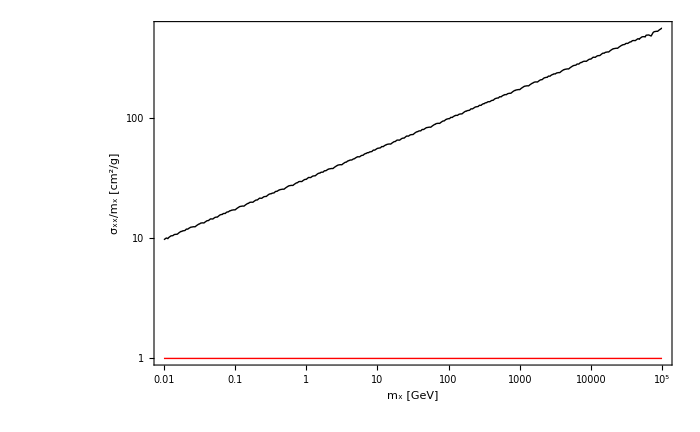
```mathematica
Show[-Graphics-,-Graphics-]
```

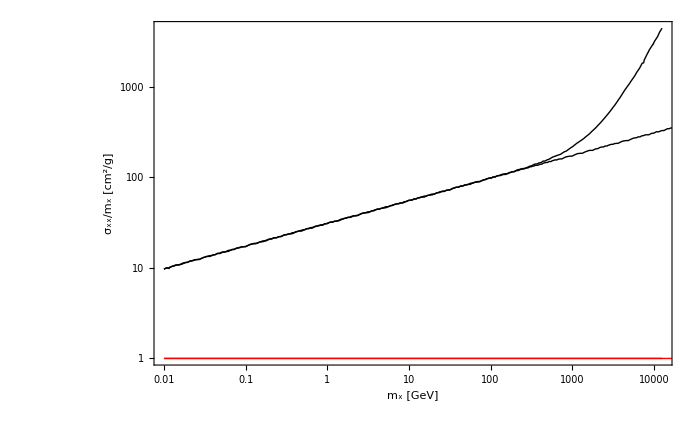

```mathematica
(*SATURATION TIME WITH ANNIHILATION *)
```

```mathematica
(*WHITE DWARF *)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
```

```mathematica
anncross=3*10^-32;(*in m^3/s*)
```

```mathematica
fMBboosted[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ; 

b[mx_,sigmadmdm_]:=sigmadmdm*ρx/mx*NIntegrate[fMBboosted[u]/u*(vesc^2-u^2),{u,0,vesc}];
```

```mathematica
Nx0[mx_,T_]:=vth[mx,T]*ρx/mx;
```

```mathematica
tsat[mx_,sigmadmdm_,T_]:=2/b[mx,sigmadmdm]*ArcTanh[(Nx0[mx,T]*sigmadmdm-π*rth[mx,T]^2)/(π*rth[mx,T]^2*(Nx0[mx,T]-b[mx,sigmadmdm]/(2*anncross/vth[mx,T]))/(b[mx,sigmadmdm]/(2*anncross/vth[mx,T]))-Nx0[mx,T]*sigmadmdm)];
```

```mathematica
ratio[mx_,sigmadmdm_,T_]:=ArcTanh[(Nx0[mx,T]*sigmadmdm-π*rth[mx,T]^2)/(π*rth[mx,T]^2*(Nx0[mx,T]-b[mx,sigmadmdm]/(2*anncross/vth[mx,T]))/(b[mx,sigmadmdm]/(2*anncross/vth[mx,T]))-Nx0[mx,T]*sigmadmdm)];(*ratio of saturation time and equilibrium time*)
```

```mathematica
tsat[10^4,10^4/(5.62*10^27),10^7]
```

7.895×10^10

```mathematica
(*WHITE DWARF WITH NUCLEI AND SELF*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=12;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
Nn=4/3*π *R^3*n;
sigmasat=(π*R^2)/Nn;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
fMB[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ; 
b[mx_,sigmadmdm_]:=sigmadmdm*ρx/mx*NIntegrate[fMB[u]/u*(vesc^2-u^2),{u,0,vesc}];
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
teq[mx_,sigma_,sigmadmdm_,T_,anncross_]:=2/((b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5);
```

```mathematica
tsat[mx_,sigma_,sigmadmdm_,T_,anncross_]:=teq[mx,sigma,sigmadmdm,T,anncross]*ArcTanh[(1/teq[mx,sigma,sigmadmdm,T,anncross]*π*rth[mx,T]^2)/(0.5*π*b[mx,sigmadmdm]*rth[mx,T]^2+a[mx,sigma]*sigmadmdm)];
```

```mathematica
ratio[mx_,sigma_,sigmadmdm_,T_,anncross_]:=ArcTanh[(1/teq[mx,sigma,sigmadmdm,T,anncross]*π*rth[mx,T]^2)/(0.5*π*b[mx,sigmadmdm]*rth[mx,T]^2+a[mx,sigma]*sigmadmdm)];
```

```mathematica
tsat[10^2,10^-48,10^2/(5.62*10^27),10^7,3*10^-32]//Quiet
```

2.39256×10^9

```mathematica
ratio[10^2,10^-48,10^2/(5.62*10^27),10^7,3*10^-32]//Quiet
```

0.584273

```mathematica
(******************************************************************************************************************************************************************************************)
```

```mathematica
(*NS CHECK WITH ZUREK MACDERMOTT*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
ρx=10^6*10^3(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
(*mphi=10;*)
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
(*asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;*)
```

```mathematica
(*a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));*)
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5},MaxRecursion->12,AccuracyGoal->5];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5},MaxRecursion->12,AccuracyGoal->5];
```

```mathematica
auni[100,sigmasat]
```

7.18413×10^26

```mathematica
agen[100,sigmasat,1]
```

6.62288×10^26

```mathematica
tage=10^10*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27)(*GeV*);
NxBEC[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*2.612*((mx*T*8.62*10^-14)/(2*π))^1.5*(5.62*10^15)^3;
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
```

```mathematica
myticks={{{{-44,"10^-40"},{-48,"10^-44"},{-52,"10^-48"},{-56,"10^-52"},{-60,"10^-56"},{-64,"10^-60"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"}},None}};
```

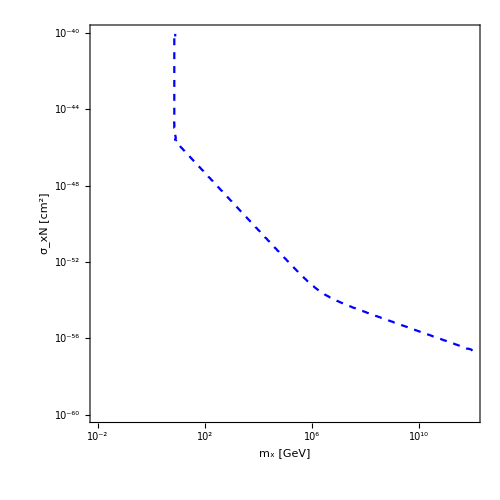

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==Nself[10^x,10^5]},{x,-2,12},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks]
```

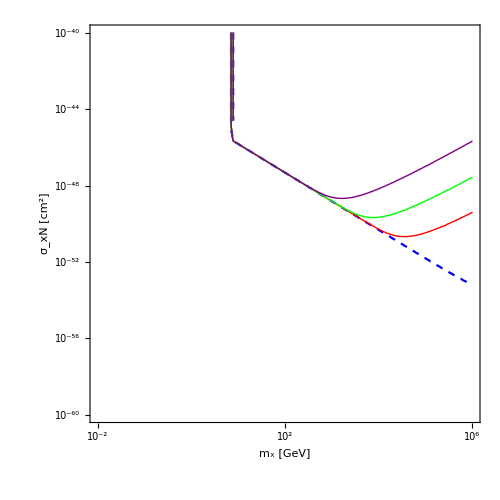

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==Nself[10^x,10^5],totcapgen[10^x,10^y,1000]==Nself[10^x,10^5],totcapgen[10^x,10^y,100]==Nself[10^x,10^5],totcapgen[10^x,10^y,10]==Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green},{Thick,Purple}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks]
```

```mathematica
(*with BEC*)
```

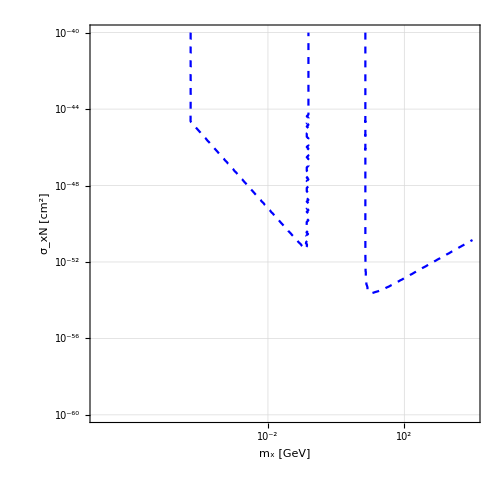

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==NchBoson[10^x]+NxBEC[10^x,10^5]},{x,-7,4},{y,-44,-64},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic,FrameTicks->myticks]
```

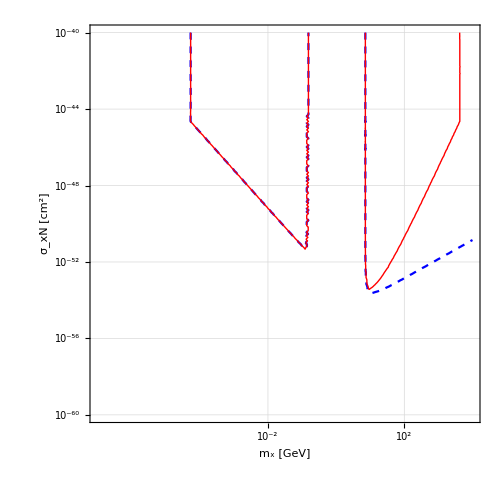

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==NchBoson[10^x]+NxBEC[10^x,10^5],totcapgen[10^x,10^y,10^-2]==NchBoson[10^x]+NxBEC[10^x,10^5]},{x,-7,4},{y,-44,-64},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic,FrameTicks->myticks]
```

```mathematica
(******************************************************************************************************************************************************************************************)
```

```mathematica
(*NS CHECK WITH ZUREK MACDERMOTT*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
ρx=10^6*0.4(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
βplus[mx_?NumericQ]:=(4*mx*mn)/(mx+mn)^2;
```

```mathematica
fMB[u_?NumericQ]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
c=3*10^8;
(*mphi=10;*)
```

```mathematica
g1[u_?NumericQ,mx_?NumericQ,mphi_?NumericQ]:=mphi^2*(1-1/βplus[mx]*(u^2/(u^2+vesc^2)))/(mphi^2+mx^2*1/βplus[mx]*(u/c)^2);
```

```mathematica
(*asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;*)
```

```mathematica
(*a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));*)
```

```mathematica
auni[mx_?NumericQ,sigma_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*(1-1/βplus[mx]*u^2/(u^2+vesc^2)),{u,0,vesc/(1/βplus[mx]-1)^0.5},MaxRecursion->12,AccuracyGoal->5];
agen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=Min[sigma,sigmasat]*ρx/mx*Min[1,δp[mx]/pf]*Nn*NIntegrate[fMB[u]/u*(vesc^2+u^2)*g1[u,mx,mphi],{u,0,vesc/(1/βplus[mx]-1)^0.5},MaxRecursion->12,AccuracyGoal->5];
```

```mathematica
auni[100,sigmasat]
```

2.87365×10^23

```mathematica
agen[100,sigmasat,1]
```

2.64915×10^23

```mathematica
tage=10^10*3.15*10^7;

rth[mx_?NumericQ,T_?NumericQ]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcapuni[mx_?NumericQ,sigma_?NumericQ]:=  auni[mx,sigma]*tage;
totcapgen[mx_?NumericQ,sigma_?NumericQ,mphi_?NumericQ]:=  agen[mx,sigma,mphi]*tage;
```

```mathematica
Nself[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27)(*GeV*);
NxBEC[mx_?NumericQ,T_?NumericQ]:=4/3*π*rth[mx,T]^3*2.612*((mx*T*8.62*10^-14)/(2*π))^1.5*(5.62*10^15)^3;
Mpl=1.2211*10^19;
NchBoson[mx_?NumericQ]:=2/π*Mpl^2/mx^2;
```

```mathematica
myticks={{{{-44,"10^-40"},{-48,"10^-44"},{-52,"10^-48"},{-56,"10^-52"},{-60,"10^-56"},{-64,"10^-60"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"}},None}};
```

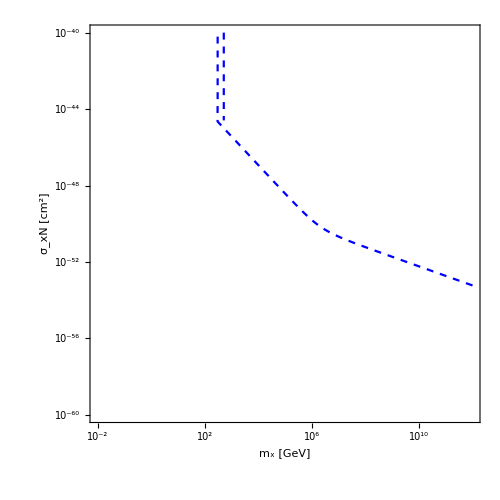

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==Nself[10^x,10^5]},{x,-2,12},{y,-44,-64},Frame->True,PlotPoints->50,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks]
```

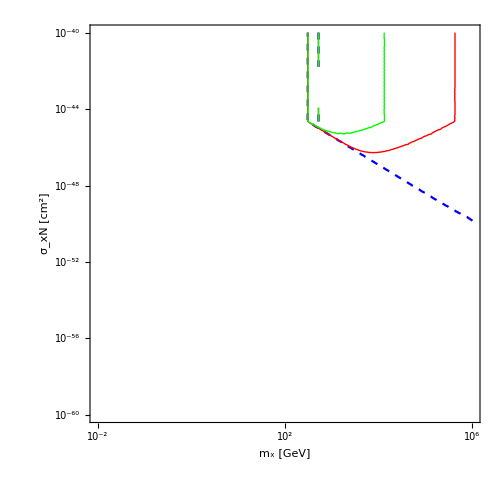

```mathematica
ContourPlot[{totcapuni[10^x,10^y]==Nself[10^x,10^5],totcapgen[10^x,10^y,100]==Nself[10^x,10^5],totcapgen[10^x,10^y,10]==Nself[10^x,10^5]},{x,-2,6},{y,-44,-64},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Dashed,Blue},{Thick,Red},{Thick,Green}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,FrameTicks->myticks]
```

```mathematica
(*NS CHECK WITH ZUREK MACDERMOTT*)
```

```mathematica
R=10.6*10^3;(*in m*)
```

```mathematica
vesc=1.8*10^8;(*in m/sec*)
vbar=220*10^3;(*in m/sec*)
```

```mathematica
Nn=1.57*10^57;
```

```mathematica
ρx=10^6*10^6(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
mn=1;(*in GeV*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*ρ/(1.6725*10^-27))^(1/3);
```

```mathematica
sigmasat=(π*R^2)/Nn;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=1.4*10^18;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
```

```mathematica
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
tage=10^10*3.15*10^7;

rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
totcap[mx_,sigma_]:=  a[mx,sigma]*tage;
```

```mathematica
Nself[mx_,T_]:=4/3*π*rth[mx,T]^3*ρ*1/(mx*1.78*10^-27)(*GeV*);
NxBEC[mx_,T_]:=4/3*π*rth[mx,T]^3*2.612*((mx*T*8.62*10^-14)/(2*π))^1.5*(5.62*10^15)^3;
Mpl=1.2211*10^19;
NchBoson[mx_]:=2/π*Mpl^2/mx^2;
```

```mathematica
myticks={{{{-44,"10^-40"},{-48,"10^-44"},{-52,"10^-48"},{-56,"10^-52"},{-60,"10^-56"},{-64,"10^-60"}},None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"},{10,"10^10"},{12,"10^12"}},None}};
```

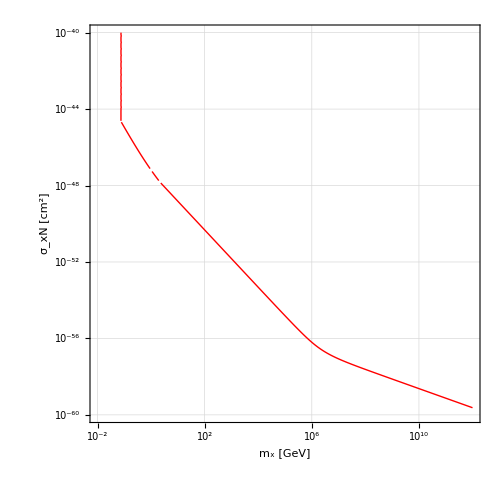

```mathematica
ContourPlot[{totcap[10^x,10^y]==Nself[10^x,10^5]},{x,-2,12},{y,-44,-64},PlotPoints->60,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic,FrameTicks->myticks]//Quiet
```

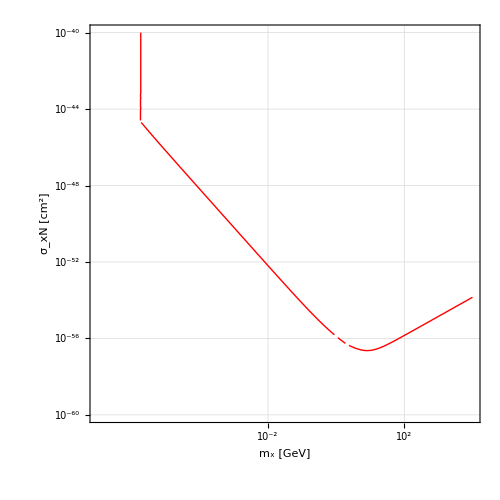

```mathematica
ContourPlot[{totcap[10^x,10^y]==NchBoson[10^x]+NxBEC[10^x,10^5]},{x,-7,4},{y,-44,-64},PlotPoints->20,Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xN [cm^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,GridLines->Automatic,FrameTicks->myticks]//Quiet
```

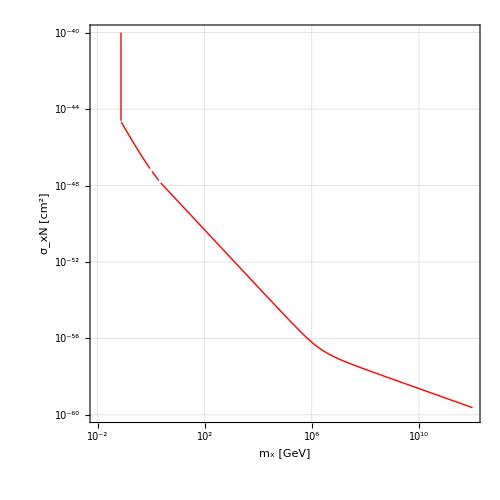
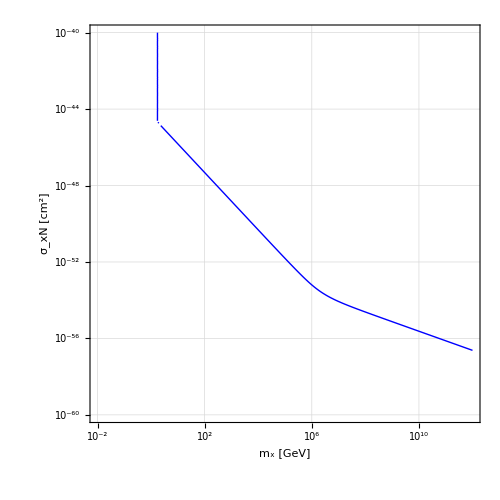
```mathematica
Show[-Graphics-,-Graphics-]
```

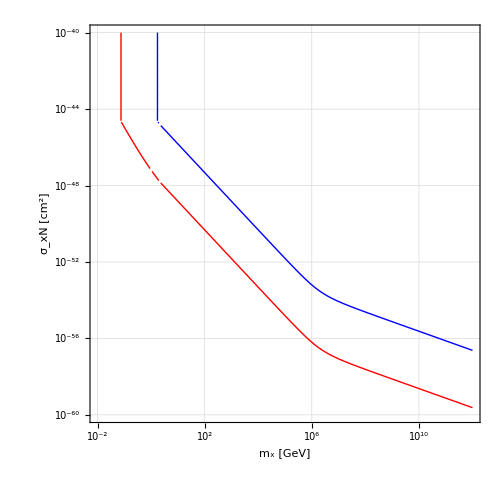

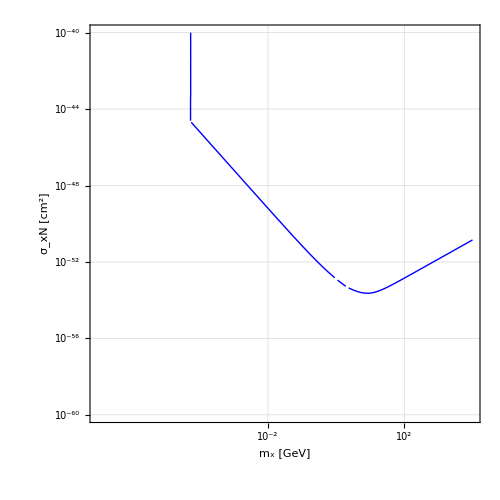
```mathematica
Show[-Graphics-,-Graphics-]
```

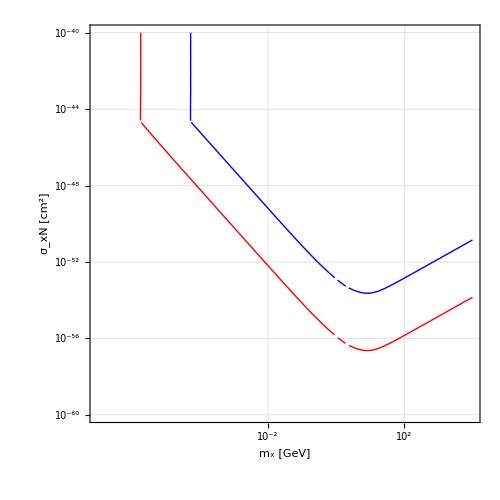

```mathematica
(*EVERYTHING IS WORKING FINE!CHECKED*)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mn=12;(*in GeV*)
mp=1;(*in GeV*)
```

```mathematica
ρx=10^6*10^3(*in GeV/m^3*)(*Due to Overdensity*);
```

```mathematica
A=12;
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
```

```mathematica
mup[mx_?NumericQ]:=(mp *mx)/(mp+mx);
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^10;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
tage=3 10^17;(*in sec*)
```

```mathematica
fMBboosted[u_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2] ;
```

```mathematica
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
sigmasat=(π*R^2)/Nn;
n=10^36;(*in m^-3*)
Nn=4/3*π *R^3*n;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
```

```mathematica
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[A^2*mr[mx]^2/mup[mx]^2*sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));(*sigma corresponds to DM-proton/neutron cross section*)
```

```mathematica
c=3*10^8;
mphi=0.01;
```

```mathematica
g1[u_,mx_]:=(mphi^2*(vesc^2-u^2))/(vesc^2+u^2)(mphi^2+mx^2*((u^2+vesc^2)/c^2))/((mphi^2+mx^2*(u/c)^2)*(mphi^2+mx^2*(vesc/c)^2));

b[mx_?NumericQ,sigmadmdm_?NumericQ]:=sigmadmdm*ρx/mx*NIntegrate[fMBboosted[u]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc}];

d[mx_?NumericQ,T_?NumericQ]:=π*rth[mx,T]^2*ρx/mx*NIntegrate[fMBboosted[u]/u*(u^2+vesc^2)*(g1[u,mx]),{u,0,vesc}];
```

```mathematica
tsat[mx_,sigmadmdm_,T_,sigma_]:=1/b[mx,sigmadmdm]*Log[(a[mx,sigma]+b[mx,sigmadmdm]*(π*rth[mx,T]^2)/sigmadmdm)/(a[mx,sigma]+Nx0[mx])];(*estimate of saturation time which is the geometrical limit of self capture*)
```

```mathematica
totcap[mx_?NumericQ,sigmadmdm_?NumericQ,T_?NumericQ,sigma_?NumericQ]:=Piecewise[{{(π*rth[mx,T]^2)/sigmadmdm+(tage-tsat[mx,sigmadmdm,T,sigma])*(a[mx,sigma]+d[mx,T]),tsat[mx,sigmadmdm,T,sigma]-tage<0},{(a[mx,sigma]/b[mx,sigmadmdm]+Nx0[mx])*Exp[b[mx,sigmadmdm]*tage]-a[mx,sigma]/b[mx,sigmadmdm],tsat[mx,sigmadmdm,T,sigma]-tage>0}}];
```

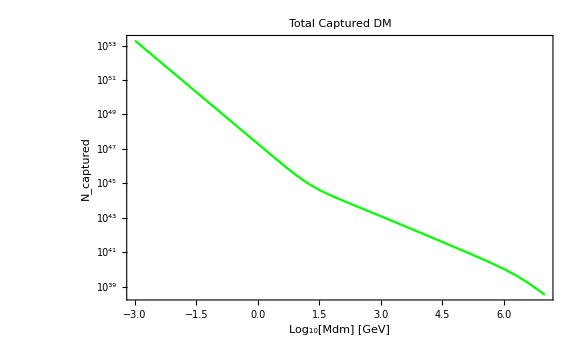

```mathematica
LogPlot[{totcap[10^x,10^x/(5.62*10^27),10^7,10^-51]},{x,-3,7},ImageSize->Large, Frame->True,FrameStyle->Directive[14,"Times",Black],AxesOrigin->{-3,0},PlotLegends->"Expressions",PlotStyle->{Red,Green},FrameLabel->{"Log_10[Mdm] [GeV]","N_captured"},PlotLabel->"Total Captured DM"]
```